# Detecting Malaria-Infected Blood Cells Using Machine Learning

Shruti Panse

Mentor: Emma Yang

## Overview

The goal of this project is to use artificial intelligence to detect Malaria. A program will be created to learn the differences between Malaria-infected and Malaria uninfected red blood cells in order to classify them by type. The program will use a neural network to classify images of cells into two classes. A data set with images of infected and uninfected red blood cells, sourced from Kaggle, will be used to train the program. Once an image is inputted, the program will run and output a diagnosis of “infected” or “uninfected” based on the results.

## Introduction

Malaria is a life-threatening disease caused by parasites that are transmitted to people through the bite of infected female Anopheles mosquitoes. Once inside the body, the Malaria parasite multiplies in the liver cells and gets released back into the bloodstream to destroy blood cells. In 2017, there were an estimated 219 million cases of Malaria in 87 countries. The symptoms of malaria include cycles of chills, fever, sweats, muscle aches and headache that recur every few days. There can also be vomiting, diarrhea, coughing, and jaundice in the skin and eyes. Even more extreme symptoms include, bleeding problems, shock, kidney and liver failure, central nervous system problems, comas, and death. A diagnosis is When detected early and accurately, such symptoms can be prevented, thus using machine learning to quickly, efficiently, and reliably diagnose malaria is important to help people stop the negative effects of malaria before it’s too late.

## Creating Training Data

Goal: To import datasets, create variables, and link images to their corresponding values.

I started my project by downloading Red Blood Cell Datasets from Kaggle. The images included Malaria infected and uninfected cell strains.

Cell images downloaded from: https://www.kaggle.com/iarunava/cell-images-for-detecting-malaria #cell _images.zip

```mathematica
infected=FileNames["*.png","C:\\Users\\Shruti Panse\\Desktop\\Shruti Panse- Wolfram Summer Camp\\WSS-Template\\Final Project\\Drafts\\cell_images\\Parasitized"];
uninfected=FileNames["*.png","C:\\Users\\Shruti Panse\\Desktop\\Shruti Panse- Wolfram Summer Camp\\WSS-Template\\Final Project\\Drafts\\cell_images\\Uninfected"];
```

Constructing File Objects for Images
	In order to optimize the speed of imports, I created file objects for the 27,000+ images so that they would import on the fly rather than importing all at once.

```mathematica
infectedIMG=File/@infected;
uninfectedIMG=File/@uninfected;
```

Generating Values for Training/Testing Data.
	I created lists of true and false values equal to the amount of images for each class of uninfected and infected. This was done so later on I could match image to value. True represented infected and false equaled uninfected.

```mathematica
Length[infected]
```

13779

```mathematica
infectedvalues=Table[True, Length[infected]];
```

```mathematica
Length[uninfected]
```

13779

```mathematica
uninfectedvalues=Table[False, Length[uninfected]];
```

Combing Infected and Uninfected Values and Keys

```mathematica
imagekeys=Flatten[{infectedIMG, uninfectedIMG}];
```

```mathematica
values=Flatten[{infectedvalues, uninfectedvalues}];
```

Creating Training/Testing Data by Combining Keys and Values
	I separated the associated data into two groups, one for training and one fro validation. The training data will be the majority, 75%, because it is what the neural net will be learning. The validation data acts as a test at the end of each training round to track the neural network’s progress, thus it is a smaller part of the data, 25%.

```mathematica
data= RandomSample[AssociationThread[imagekeys-> values]];
```

```mathematica
traininglength= Length[data]*.75
```

20668.5

```mathematica
20668.5
```

20668.5

```mathematica
trainingdata= data[[1;;20669]];
```

```mathematica
validationdata=data[[20670;;]];
```

## Training the Neural Network

Goal: To create a Neural Network using the NetChain function with multiple layers within it.

Creating the Baseline Neural Network with Layers
	In order to sense the difference between cells with Malaria and cells without Malaria, layers need to be put into place to control the features that the neural net senses and organize them into classes.
	 Here are a few notable layers:
		ResizeLayer: Changes the dimensions of each image to make them all even for the neural network.
		Ramp: Narrows the number of features detected by getting rid of unessential features.
		PoolingLayer: Downsamples the features detected.
		FlattenLayer: Creates features into a feature vector.
		SoftmaxLayer: Turns the vectors into a probability to classify the image.

```mathematica
dims= {135,135}
```

{135,135}

```mathematica
lenet=NetChain[{
ResizeLayer[dims],
ConvolutionLayer[20,5],
Ramp, (*Takes out the the not useful features*)
PoolingLayer[2,2],(*Downsamples*)

ConvolutionLayer[50,5],
Ramp, (*Takes out the the not useful features*)
PoolingLayer[2,2],(*Downsamples*)

FlattenLayer[],500,(*Makes features into feature vector"*)
Ramp,2,(*Takes out the the not useful features- True or false*)
SoftmaxLayer[]},(*Turns the vector into probabilities*)
"Output"->NetDecoder[{"Class",{True,False}}],(*Tensor into true or false*)
"Input"->NetEncoder["Image"](*Turns image into numbers*)
]
```

NetChain[<>]

Training the Neural Network with Net Train
	In order to train the neural network, I used a GPU, graphics processing device, to run the data with 10 rounds. The error rate for the round training was 0.329% while the validation training error rate was 7.53%. The gap between the orange round training and blue validation training represents the amount of overfitting. The smaller the gap, the less overfitting. Furthermore, the downward trend of the round training shows the error rate going down as the neural network goes through more rounds.

```mathematica
results=NetTrain[lenet,Normal[trainingdata],All,ValidationSet->Normal[validationdata],MaxTrainingRounds->10, TargetDevice->"GPU"]
```

NetTrain Results
summary | ,,  batches:3230  rounds:10  time:2.1min  examples/s:1612
data | ,,  training examples:20669  validation examples:6889  processed examples:206720  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.11×10^-2  error:0.329%
validation | ,,  loss:4.1×10^-1  error:7.53%
 | 
-Graphics-  training set	-Graphics-  validation set |

## Creating and Training Augmented Dataset

After training with the regular dataset , I needed to train with new data to prevent overfitting and strengthen my network. However, I did not have another dataset with different  blood cell images. So, I created an augmented dataset, which takes the images in the first dataset and makes slight changes to make them appear as different images to the neural network. I trained the neural network using the new augmented data. I used the random crop augmentation to change the images slightly. First I increased the dimensions of each image by 4 pixels and set the end dimensions to 135 by 135, so that the random crop would be able to have freedom in cropping each image but still adhere to the dimensions of the other images. Once again, I used the NetChain function with the same layers as before to narrow down the features detected.

```mathematica
augment=ImageAugmentationLayer[{135,135},
"Input"-> NetEncoder[{"Image",{139,139}}],"Output"-> NetDecoder["Image"]]
```

ImageAugmentationLayer[<>]

```mathematica
augment[-Graphics-]
```

-Graphics-

```mathematica
dims2={139,139}
```

{139,139}

```mathematica
lenet2=NetChain[{
ResizeLayer[dims2],
ImageAugmentationLayer[{135,135}],
ConvolutionLayer[20,5],
Ramp,
PoolingLayer[2,2],
ConvolutionLayer[50,5],
Ramp,
PoolingLayer[2,2],
FlattenLayer[],500,
Ramp,2,
SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",{True,False}}],
"Input"->NetEncoder["Image"]
]
```

NetChain[<>]

Training the Augmented Dataset
	For this training set, I used CPU and went through 7 rounds. The error rate for the round training was 3.72% while the validation training error was 5.84%. The gap between the orange and blue lines shows that there was limited overfitting the augmented dataset. Furthermore, the downward trend of the round training shows the error rate going down as the neural network goes through more rounds.

```mathematica
results2=NetTrain[lenet2,Normal[trainingdata],All,ValidationSet->Normal[validationdata],MaxTrainingRounds->7]
```

NetTrain Results
summary | ,,  batches:2261  rounds:7  time:1.1h  examples/s:37.
data | ,,  training examples:20669  validation examples:6889  processed examples:144704  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.05×10^-1  error:3.72%
validation | ,,  loss:1.87×10^-1  error:5.84%
 | 
-Graphics-  training set	-Graphics-  validation set |

## Extracting the Training Net from Training Results

Taking the trained neural network and preparing it for testing.

```mathematica
trained=results2["TrainedNet"]
```

NetChain[<>]

```mathematica
Export["augmentnet.wlnet",trained]
```

augmentnet.wlnet

```mathematica
trained2=results["TrainedNet"]
```

NetChain[<>]

```mathematica
Export["nonaugmentnet.wlnet",trained2]
```

nonaugmentnet.wlnet

```mathematica
trained=Import["C:\\Users\\Shruti Panse\\Desktop\\Shruti Panse- Wolfram Summer Camp\\WSS-Template\\Final Project\\augmentnet.wlnet"]
```

```mathematica
NetChain[<>]
```

## Creating Visualizations

To display the results of training and testing, I created a ConfusionMatrixPlot to visually represent the success of the neural net. I used the function ClassifierMeasurements to make the matrix. The orange colored boxes represent the times that the actual answer and the machine prediction were the same. There were 3336 times that the actual and machine predicted answer were true and 3344 times that the predicted and actual answer were false. So, because they are close, this means that the neural network did not prefer true over false. I also added in extra information such as the  Accuracy, Precision, and WorstClassifiedExamples to provide more information about the neural network. In conclusion, the neural network had 97% accuracy for both detecting malaria infected and uninfected cells.

```mathematica
testset= Import/@Keys[validationdata];
```

```mathematica
visual= ClassifierMeasurements[trained, Normal[RandomSample[AssociationThread[testset-> Values[validationdata]]]]]
```

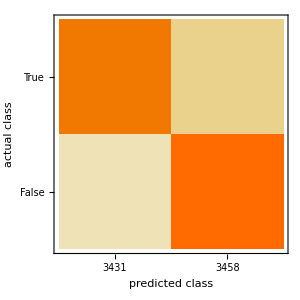
0.969662 |  |  |  |  |  |  |  |  | 
<|True→0.969627,False→0.969697|> |  |  |  |  |  |  |  |  | 
-Graphics- |  |  |  |  |  |  |  |  | 
<|True→0.972311,False→0.967033|> |  |  |  |  |  |  |  |  | 
<|True→0.966957,False→0.972376|> |  |  |  |  |  |  |  |  | 
<|True→0.966957,False→0.972376|> |  |  |  |  |  |  |  |  | 
<|True→0.0276243,False→0.0330435|> |  |  |  |  |  |  |  |  | 
-Graphics-→False | -Graphics-→True | -Graphics-→False | -Graphics-→True | -Graphics-→True | -Graphics-→True | -Graphics-→True | -Graphics-→False | -Graphics-→True | -Graphics-→False

```mathematica
visual/@{"Accuracy","FScore","ConfusionMatrixPlot","Precision","Recall","Sensitivity","FalsePositiveRate","WorstClassifiedExamples"}//TableForm
```